# Chimera: Chiral Measures Research Assistant

© Emilio Pisanty 2024

## Introduction

### Readme

The Mathematica package Chimera – Chiral Measures Research Assistant – contains code and tools useful to quantify the chirality of a distribution, and to apply those tools to photoelectron momentum spectra, such as might be obtained from strong-field ionization of chiral molecules, or of achiral systems driven by chiral fields.

(Expand the cell below for a brief package description which will be included in the package .m file)
TO DO: update this

```mathematica
(* Chimera: Chiral Measures Research Assistant *)
(* © Emilio Pisanty, 2024 *)

(* For more information, see https://github.com/????/???? *)

(*TODO - update this*)
```

### TO DO

- Update SphericalHarmonicS to reflect the new normalization.
- Add Private brackets to all code.
- Check all functions have usage statements.
- Pull in helixDataDistribution as well as three-gaussians distributions.
- Replace all the code based on ClebschGordan and replace it with ThreeJSymbol

### Licensing

This package is licensed under ?????.

## Implementation

## Initialization

### Initialization and most package infrastructure

#### Package initialization

```mathematica
BeginPackage["Chimera`"];
```

#### Version number

The variable $ChimeraVersion gives the version of the Chimera package currently loaded, and its timestamp

```mathematica
$ChimeraVersion::usage="$ChimeraVersion prints the current version of the Chimera package in use and its timestamp.";
$ChimeraTimestamp::usage="$ChimeraTimestamp prints the timestamp of the current version of the Chimera package.";
Begin["`Private`"];
$ChimeraVersion:="Chimera v0.1, "<>$ChimeraTimestamp;
End[];
```

The timestamp is updated every time the notebook is saved via an appropriate notebook option, which is set by the code below.

```mathematica
SetOptions[
EvaluationNotebook[],
NotebookEventActions->{{"MenuCommand","Save"}:>(
NotebookWrite[
Cells[CellTags->"version-timestamp"]⟦1⟧,
Cell[
BoxData[RowBox[{"Begin[\"`Private`\"];$ChimeraTimestamp=\""<>DateString[]<>"\";End[];"}]]
,"Input",InitializationCell->True,CellTags->"version-timestamp"
],None,AutoScroll->False];
NotebookSave[]
),PassEventsDown->True}
];
```

To reset this behaviour to normal, evaluate the cell below

```mathematica
SetOptions[EvaluationNotebook[],NotebookEventActions->{{"MenuCommand","Save"}:>(NotebookSave[]),PassEventsDown->True}]
```

#### Directory

```mathematica
$ChimeraDirectory::usage="$ChimeraDirectory is the directory where the current Chimera package instance is located.";
```

```mathematica
Begin["`Private`"];
With[{softLinkTestString=StringSplit[StringJoin[ReadList["! ls -la "<>StringReplace[$InputFileName,{" "->"\\ "}],String]]," -> "]},
If[Length[softLinkTestString]>1,(*Testing in case $InputFileName is a soft link to the actual directory.*)
$ChimeraDirectory=StringReplace[DirectoryName[softLinkTestString⟦2⟧],{" "->"\\ "}],
$ChimeraDirectory=StringReplace[DirectoryName[$InputFileName],{" "->"\\ "}];
]];
End[];
```

#### Git commit hash and message

```mathematica
$ChimeraCommit::usage="$ChimeraCommit returns the git commit log at the location of the Chimera package if there is one.";
$ChimeraCommit::OS="$ChimeraCommit has only been tested on Linux.";
```

```mathematica
Begin["`Private`"];
$ChimeraCommit:=(If[$OperatingSystem≠"Unix",Message[$ChimeraCommit::OS]];
StringJoin[Riffle[ReadList["!cd "<>$ChimeraDirectory<>" && git log -1",String],{"\n"}]]);
End[];
```

### Timestamp

#### Timestamp

```mathematica
Begin["`Private`"];$ChimeraTimestamp="Sat 22 Jun 2024 17:27:17";End[];
```

### Usage of the package-infrastructure variables

```mathematica
$ChimeraVersion
```

Chimera v1.0.0, Mon 13 Feb 2023 17:44:42

```mathematica
$ChimeraTimestamp
```

Mon 13 Feb 2023 17:44:42

```mathematica
$ChimeraDirectory
```

The $ChimeraCommit command only works if you have a working git repository on the same directory as the notebook file. It also (so far) only works on Linux.

```mathematica
$ChimeraCommit
```

## Package code

### General functions

#### SolidHarmonicS - NEEDS UPDATING

This function implements the solid harmonic S_(l,m)(r)=r^l Y_(l,m)(θ,ϕ), which is a homogeneous polynomial of degree l, and lends itself much better to symbolic differentiation than explicit spherical harmonics.

Code provided by J.M. at http://mathematica.stackexchange.com/a/124336/1000 under the WTFPL. This version was copied from the RBSFA package, which lives at https://github.com/episanty/RB-SFA.

```mathematica
SolidHarmonicS::usage="SolidHarmonicS[l,m,x,y,z] calculates the solid harmonic S_lm(x,y,z)=r^lY_lm(x,y,z).

SolidHarmonicS[l,m,{x,y,z}] does the same.";
Begin["`Private`"];
SolidHarmonicS[λ_Integer,μ_Integer,x_,y_,z_]/;λ≥Abs[μ]:=Sqrt[(2 λ+1)/(4 π)] Sqrt[Gamma[λ-Abs[μ]+1]/Gamma[λ+Abs[μ]+1]] 2^-λ (-1)^((μ-Abs[μ])/2)×
If[Rationalize[μ]==0,1,(x+Sign[μ]ⅈ y)^Abs[μ]]×
Sum[
(-1)^(μ+k) Binomial[λ,k] Binomial[2 λ-2 k,λ] Pochhammer[λ-Abs[μ]-2 k+1,Abs[μ]] ×
If[TrueQ[Pochhammer[λ-Abs[μ]-2 k+1,Abs[μ]]==0],1,
If[Rationalize[k]==0,1,(x^2+y^2+z^2)^k]If[Rationalize[λ-Abs[μ]-2 k]==0,1,z^(λ-Abs[μ]-2 k)]
]
,{k,0,Quotient[λ,2]}]
SolidHarmonicS[λ_Integer,μ_Integer,{x_,y_,z_}]/;λ≥Abs[μ]:=SolidHarmonicS[λ,μ,x,y,z]
End[];
```

One example:

```mathematica
SolidHarmonicS[4,2,{x,y,z}]
```

((x+ⅈ y)^2 (840 z^2-120 (x^2+y^2+z^2)))/(64 √(10 π))

#### cleanContourPlot

This function cleans up automatically generated contour plots. Generically, a contour plot is made of a Polygon with a vast number of vertices in its interior, which are not necessary and only slow the plot down - including a large use of CPU when the mouse hovers above it, which is definitely unwanted. (In addition, these polygons can give rise to white edges inside each contour when printed to pdf, which is also undesirable.) This function changes such Polygons to FilledCurve constructs which no longer contain the unwanted mid-contour points.

This function was written by Szabolcs Horvát (http://mathematica.stackexchange.com/users/12/szabolcs) and was originally posted at http://mathematica.stackexchange.com/a/3279 under a CC-BY-SA license.

```mathematica
cleanContourPlot::usage="cleanContourPlot[plot] Cleans up a contour plot by coalescing complex polygons into single FilledCurve instances. See MM.SE/a/3279 for source and documentation.";
```

```mathematica
Begin["`Private`"];
cleanContourPlot[cp_] :=
 Module[{points, groups, regions, lines},
  groups = 
   Cases[cp, {style__, g_GraphicsGroup} :> {{style}, g}, Infinity];
  points = 
   First@Cases[cp, GraphicsComplex[pts_, ___] :> pts, Infinity];
  regions = Table[
    Module[{group, style, polys, edges, cover, graph},
     {style, group} = g;
     polys = Join @@ Cases[group, Polygon[pt_, ___] :> pt, Infinity];
     edges = Join @@ (Partition[#, 2, 1, 1] & /@ polys);
     cover = Cases[Tally[Sort /@ edges], {e_, 1} :> e];
     graph = Graph[UndirectedEdge @@@ cover];
     {Sequence @@ style, 
      FilledCurve[
       List /@ Line /@ First /@ 
          Map[First, 
           FindEulerianCycle /@ (Subgraph[graph, #] &) /@ 
             ConnectedComponents[graph], {3}]]}
     ],
    {g, groups}];
  lines = Cases[cp, _Tooltip, Infinity];
  Graphics[GraphicsComplex[points, {regions, lines}], 
   Sequence @@ Options[cp]]
  ]
End[];
```

### Photoelectron spectra

#### photoElectronSpectrumList

```mathematica
photoElectronSpectrumList::usage="photoElectronSpectrumList[data,range,Δp] returns a histogram photoelectron spectrum for the data sets data[h], where h covers the given range, using bin width Δp.";

photoElectronSpectrumList[dataSet_,range_,pBin_,options___]:=Map[photoElectronSpectrum[dataSet[#],pBin,options,PlotLabel->#]&,range]
```

#### photoElectronSpectrum

```mathematica
photoElectronSpectrum::usage="photoElectronSpectrum[data,Δp] returns a histogram photoelectron spectrum for the given data set, which must be in the standard format, using bin width Δp.";

photoElectronSpectrum[dataSet_,pBin_,options___]:=Block[{dataSet2,histogramAssoc},
If[
Dimensions[dataSet][[2]]==5,
dataSet2=dataSet,
dataSet2=Map[Join[#,{Norm[#[[1;;3]]]}]&,dataSet]
];
histogramAssoc=Map[
Total,
KeySort[GroupBy[dataSet2,Floor[#[[5]],pBin]&]][[1;;,All,4]]
];
Show[{
Graphics[{
EdgeForm[{Opacity[0.665],Thickness[Small]}],
FaceForm[RGBColor[0.987148, 0.8073604000000001, 0.49470040000000004]],
KeyValueMap[
Function[{p,value},Rectangle[{p,0},{p+pBin,value}]],
histogramAssoc
]
}]
}
,options
,Frame->True
,ImageSize->400
,AspectRatio->1/1.6
,PlotRangePadding->{{None,None},{None,Scaled[0.07]}}
]
]
```

### Spherical decomposition

#### Testing symmetry of spherical harmonics

From the SphericalHarmonicY docs: “For l≥0, Y_l^m(θ,ϕ)=√((2l+1)/(4π))√((l-m)!/(l+m)!)P_l^m(cos(θ))e^imϕ where P_l^m is the associated Legendre function. “

First off: a sanity check to make sure that SphericalHarmonicY and SolidHarmonicS do indeed match.

```mathematica
Table[Table[
Simplify[
SphericalHarmonicY[ℓ,m,θ,ϕ]==SolidHarmonicS[ℓ,m,FromSphericalCoordinates[{1,θ,ϕ}]]
]
,{m,-ℓ,ℓ}],{ℓ,0,4}]
```

{{True},{True,True,True},{True,True,True,True,True},{True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True}}

The symmetry of the spherical harmonics: changing the sign of m is equivalent to conjugation with a global sign of (-1)^m.

```mathematica
Table[Table[
Simplify[
(-1)^m SphericalHarmonicY[ℓ,m,θ,ϕ]*==SphericalHarmonicY[ℓ,-m,θ,ϕ]
,Assumptions->{{θ,ϕ}>0}
]
,{m,0,ℓ}],{ℓ,0,5}]
```

{{True},{True,True},{True,True,True},{True,True,True,True},{True,True,True,True,True},{True,True,True,True,True,True}}

The (-1)^m sign comes from the Legendre factor P_ℓ^m(cos(θ)):

```mathematica
Table[Table[
Sign[Simplify[
LegendreP[ℓ,m,Cos[θ]]/LegendreP[ℓ,-m,Cos[θ]]
]]
,{m,0,ℓ}],{ℓ,0,5}]
```

{{1},{1,-1},{1,-1,1},{1,-1,1,-1},{1,-1,1,-1,1},{1,-1,1,-1,1,-1}}

#### SetSphericalDecomposition

```mathematica
SetSphericalDecomposition::usage="SetSphericalDecomposition[ρSymbol,dataSet] creates memoizable definitions for ρSymbol[h,ℓ,m,{pmin,pmax}] to be the spherical decomposition with angular-momentum numbers ℓ,m over momentum bin {pmin,pmax} for the dataset dataSet[h].";

SetSphericalDecomposition[ρSymbol_,dataSet_]:=Block[{},
ρSymbol::usage=StringJoin[
ToString[ρSymbol],
"[h,ℓ,m,{pmin,pmax}] memoizes and returns the spherical decomposition with angular-momentum numbers ℓ,m over momentum bin {pmin,pmax} for the dataset ",
ToString[dataSet],
"[h]."
];
SetSharedFunction[ρSymbol];

ρSymbol[h_,ℓ_,m_/;(m>=0),{pmin_,pmax_}]:=Parallel`Developer`SendBack[
ρSymbol[h,ℓ,m,{pmin,pmax}]=Block[{momentumFilteredData},
momentumFilteredData=Select[dataSet[h],pmin<#[[5]]<pmax&];
1/electronCount[dataSet,h] Sum[
record[[4]]SolidHarmonicS[ℓ,m,record[[1;;3]]]*
,{record,momentumFilteredData}]
]
];
ρSymbol[h_,ℓ_,m_/;(m<0),{pmin_,pmax_}]:=(-1)^m Conjugate[ρSymbol[h,ℓ,-m,{pmin,pmax}]]
]
```

The Parallel`Developer`SendBack[] call is to ensure proper parallelization of the memoized definitions, as per https://mathematica.stackexchange.com/a/125307/1000

#### SetExactSphericalDecomposition

```mathematica
Options[SetExactSphericalDecomposition]=Options[NIntegrate];

SetExactSphericalDecomposition::usage="SetExactSphericalDecomposition[ρSymbol,PDF] creates memoizable definitions for ρSymbol[h,ℓ,m,{pmin,pmax}] to be the spherical decomposition with angular-momentum numbers ℓ,m over momentum bin {pmin,pmax} for the symbolic probability density function PDF[h].";

SetExactSphericalDecomposition[ρSymbol_,PDF_,options:OptionsPattern[]]:=Block[{},
ρSymbol::usage=StringJoin[
ToString[ρSymbol],
"[h,ℓ,m,{pmin,pmax}] memoizes and returns the spherical decomposition with angular-momentum numbers ℓ,m over momentum bin {pmin,pmax}, numerically integrated for the PDF ",
ToString[PDF],
"[h]."
];
ρSymbol::integrationError="Encountered integration errors in the calculation of "<>ToString[ρSymbol]<>" with parameters {h,ℓ,m,{pmin,pmax}}= `1`.";
ρSymbol::integrating="Beginning numerical integration for "<>ToString[ρSymbol]<>"[`1`,`2`,`3`,`4`]";
Off[ρSymbol::integrating];
SetSharedFunction[ρSymbol];

ρSymbol[h_,ℓ_,m_/;(m>=0),{pmin_,pmax_}]:=Parallel`Developer`SendBack[
ρSymbol[h,ℓ,m,{pmin,pmax}]=Block[{pdf,fromSphericalCoordinates,integral},
pdf[{p_,θ_,ϕ_}]:=PDF[h][p,θ,ϕ];
fromSphericalCoordinates[{pp_,θ_,ϕ_}]=FromSphericalCoordinates[{pp,θ,ϕ}];
Message[ρSymbol::integrating,h,ℓ,m,{pmin,pmax}];

Check[
integral=NIntegrate[
Times[
pdf[fromSphericalCoordinates[{p,θ,ϕ}]],
SolidHarmonicS[ℓ,m,fromSphericalCoordinates[{p,θ,ϕ}]]*,
p^2 Sin[θ]
],{θ,0,π},{ϕ,0,2π},{p,pmin,pmax}
,Evaluate[Sequence@@FilterRules[{options},Options[NIntegrate]]]
],
Message[ρSymbol::integrationError,{h,ℓ,m,{pmin,pmax}}];
integral
]
]
];
ρSymbol[h_,ℓ_,m_/;(m<0),{pmin_,pmax_}]:=(-1)^m Conjugate[ρSymbol[h,ℓ,-m,{pmin,pmax}]]
]
```

Note the use of an explicit symbolic version of fromSphericalCoordinates. This is to avoid errors thrown up by the standard FromSphericalCoordinates[{p,θ,ϕ}] when ϕ∈(π,2π) and when ϕ=-π.

#### SetSymbolicSphericalDecomposition

```mathematica
Options[SetSymbolicSphericalDecomposition]={Assumptions->{}}(*Options[NIntegrate]*);

SetSymbolicSphericalDecomposition::usage="SetSymbolicSphericalDecomposition[ρSymbol,distribution] creates memoizable definitions for ρSymbol[ℓ,m] to be the spherical decomposition with angular-momentum numbers ℓ,m over momentum space for the given symbolic distribution.";

SetSymbolicSphericalDecomposition[ρSymbol_,distribution_,options:OptionsPattern[]]:=Block[{},
ρSymbol::usage=StringJoin[
ToString[ρSymbol],
"[ℓ,m] memoizes and returns the spherical decomposition with angular-momentum numbers ℓ,m, symbollically calculated for the distribution ",
ToString[distribution],
"."
];
(*ρSymbol::integrationError="Encountered integration errors in the calculation of "<>ToString[ρSymbol]<>" with parameters {h,ℓ,m}= `1`.";*)
ρSymbol::integrating="Beginning symbolic integration for "<>ToString[ρSymbol]<>"[`1`,`2`]";
Off[ρSymbol::integrating];
SetSharedFunction[ρSymbol];

ρSymbol[ℓ_,m_/;(m>=0)]:=Parallel`Developer`SendBack[
ρSymbol[ℓ,m]=Block[{px,py,pz},
Message[ρSymbol::integrating,ℓ,m];
Expectation[
SolidHarmonicS[ℓ,m,{px,py,pz}]/.{ⅈ->-ⅈ},
{px,py,pz}\[Distributed]distribution
]
]
];
ρSymbol[ℓ_,m_/;(m<0)]:=Simplify[
(-1)^m Conjugate[ρSymbol[ℓ,-m]]
,Assumptions->OptionValue[Assumptions]
]
]
```

```mathematica
ClearAll[ρSyntheticSymbolicL];
SetSymbolicSphericalDecomposition[ρSyntheticSymbolicL,syntheticDataDistribution["L"]]
```

```mathematica
Table[m->AbsoluteTiming[ρSyntheticSymbolicL[2,m]],{m,-2,2}]
```

{-2→{0.0722775,0.0206013},-1→{0.0494435,0},0→{0.0499457,0.275442},1→{0.0473495,0},2→{0.0491292,0.0206013}}

```mathematica
ClearAll[ρHelixSymbolic2];
SetSymbolicSphericalDecomposition[ρHelixSymbolic2,helixDataDistribution[2,{px0,σ1,σ2,α}],Assumptions->helixDataAssumptions]
```

```mathematica
Table[m->AbsoluteTiming[ρHelixSymbolic2[2,m]],{m,-2,2}]
```

{-2→{0.061174,1/8 √(15/(2 π)) (2 px0^2+σ1^2-σ2^2+(-σ1^2+σ2^2) Cos[2 α])},-1→{0.0389874,0},0→{0.0446311,-1/8 √(5/π) (2 px0^2+σ1^2-σ2^2+3 σ1^2 Cos[2 α]-3 σ2^2 Cos[2 α])},1→{1.8×10^-6,0},2→{1.7×10^-6,1/8 √(15/(2 π)) (2 px0^2+σ1^2-σ2^2-σ1^2 Cos[2 α]+σ2^2 Cos[2 α])}}

```mathematica
helixDataAssumptions
```

{(px0|α)∈ℝ,{σ1,σ2}>0}

#### ρ1mToCartesian

Getting the cartesian components out of the solid harmonics:

```mathematica
Simplify[√((2π)/3)(SolidHarmonicS[1,1,{x,y,z}]-SolidHarmonicS[1,-1,{x,y,z}])/-1]
Simplify[√((2π)/3)(SolidHarmonicS[1,1,{x,y,z}]+SolidHarmonicS[1,-1,{x,y,z}])/-ⅈ]
√((4π)/3)SolidHarmonicS[1,0,{x,y,z}]
```

x

y

z

.... buuuuut, the definition of ρ_(ℓ m) involves Y_(ℓ m)(θ,ϕ)*, i.e. against the conjugate, so we need to include that.

```mathematica
Simplify[√((2π)/3)(SolidHarmonicS[1,1,{x,y,z}]*-SolidHarmonicS[1,-1,{x,y,z}]*)/-1,Assumptions->{{x,y,z}∈Reals}]
Simplify[√((2π)/3)(SolidHarmonicS[1,1,{x,y,z}]*+SolidHarmonicS[1,-1,{x,y,z}]*)/ⅈ,Assumptions->{{x,y,z}∈Reals}]
Simplify[√2 √((2π)/3)SolidHarmonicS[1,0,{x,y,z}]*,Assumptions->{{x,y,z}∈Reals}]
```

x

y

z

```mathematica
ρ1mToCartesian[{ρ1m1_,ρ10_,ρ11_}]:=Chop[√((2π)/3){(ρ11-ρ1m1)/-1,(ρ11+ρ1m1)/ⅈ,√2 ρ10}]
```

#### ρToCenterOfMass

```mathematica
2 √π SolidHarmonicS[0,0,{x,y,z}]
```

1

```mathematica
ρToCenterOfMass[{{ρ00_},{ρ1m1_,ρ10_,ρ11_}}]:=Chop[(√((2π)/3){(ρ11-ρ1m1)/-1,(ρ11+ρ1m1)/ⅈ,√2 ρ10})/(2 √π ρ00)]
```

This form for the input is to allow a natural calculation for the ρ inside:

```mathematica
ρToCenterOfMass[
Table[Table[
ρ[ℓ,m,p]
,{m,-ℓ,ℓ}],{ℓ,0,1}]
]
```

#### COM exact

```mathematica
FromSphericalCoordinates[{p,θ,ϕ}]
```

{p Cos[ϕ] Sin[θ],p Sin[θ] Sin[ϕ],p Cos[θ]}

```mathematica
ClearAll[COMfromPDF];

Options[COMfromPDF]=Join[{PrecisionGoal->8,AccuracyGoal->8},DeleteCases[Options[NIntegrate],Alternatives[PrecisionGoal->_,AccuracyGoal->_]]];

COMfromPDF::integrationError="Encountered integration errors in the calculation of COMfromPDF with pdf `1` and {pmin,pmax}= `2`.";

SetSharedFunction[COMfromPDF];

COMfromPDF[PDF_,{pmin_,pmax_},options:OptionsPattern[]]:=COMfromPDF[PDF,{pmin,pmax},options]=Block[{pdf,fromSphericalCoordinates,integrals},
pdf[{p_,θ_,ϕ_}]:=PDF[p,θ,ϕ];
fromSphericalCoordinates[{pp_,θ_,ϕ_}]=FromSphericalCoordinates[{pp,θ,ϕ}];

Check[
integrals=NIntegrate[
Times[
pdf[fromSphericalCoordinates[{p,θ,ϕ}]],
Join[{1},fromSphericalCoordinates[{p,θ,ϕ}]],
p^2 Sin[θ]
],{θ,0,π},{ϕ,-π,π},{p,pmin,pmax}
,Evaluate[Sequence@@FilterRules[{options},Options[NIntegrate]]]
];,
Message[COMfromPDF::integrationError,PDF,{pmin,pmax}];
];

;

integrals[[2;;4]]/integrals[[1]]
]
```

```mathematica
COMfromPDF[syntheticDataPDF["L"],{0.4,0.5}]
```

{0.165329,0.084463,0.038889}

Note the use of an explicit symbolic version of fromSphericalCoordinates. This is to avoid errors thrown up by the standard FromSphericalCoordinates[{p,θ,ϕ}] when ϕ∈(π,2π) and when ϕ=-π.

#### COM exact, cartesian

```mathematica
ClearAll[COMfromPDFcartesian];

Options[COMfromPDFcartesian]=Join[{PrecisionGoal->8,AccuracyGoal->8},DeleteCases[Options[NIntegrate],Alternatives[PrecisionGoal->_,AccuracyGoal->_]]];

COMfromPDFcartesian::integrationError="Encountered integration errors in the calculation of COMfromPDFcartesian with pdf `1` and {pmin,pmax}= `2`.";

COMfromPDFcartesian::integrating="Beginning numerical integration for COMfromPDFcartesian[`1`,`2`]";
(*Off[COMfromPDFcartesian::integrating];*)

SetSharedFunction[COMfromPDFcartesian];

COMfromPDFcartesian[PDF_,{pmin_,pmax_},options:OptionsPattern[]]:=COMfromPDFcartesian[PDF,{pmin,pmax},options]=Block[{integrals},
Message[COMfromPDFcartesian::integrating,PDF,{pmin,pmax}];

Check[
integrals=NIntegrate[
Times[
PDF[px,py,pz],
{1,px,py,pz},
Boole[pmin^2<px^2+py^2+pz^2<pmax^2]
],{px,-pmax,pmax},{py,-pmax,pmax},{pz,-pmax,pmax}
,Evaluate[Sequence@@FilterRules[{options},Options[NIntegrate]]]
];,
Message[COMfromPDFcartesian::integrationError,PDF,{pmin,pmax}];
];

;

integrals[[2;;4]]/integrals[[1]]
]
```

```mathematica
Off[COMfromPDFcartesian::integrating]
```

```mathematica
On[COMfromPDFcartesian::integrating]
```

```mathematica
COMfromPDFcartesian[exaggeratedDataPDF["L"],{0.6,0.7}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.54208×10^-8-2.32074×10^-34 ⅈ and 1.39892×10^-9 for the integral and error estimates.

COMfromPDFcartesian::integrationError: Encountered integration errors in the calculation of COMfromPDFcartesian with pdf exaggeratedDataPDF[L] and {pmin,pmax}= {0.6,0.7}.

{0.402821,0.00890088,4.04581×10^-6}

.... this seems to be too slow to be worth using...

### Chirality measures

#### SetChiralityMeasure

```mathematica
ClearAll[SetChiralityMeasure]
```

```mathematica
SetChiralityMeasure::usage="SetChiralityMeasure[χSymbol,ρSymbol] creates memoizable definitions for χSymbol[h,{ℓ1,ℓ2,ℓ3},{p1,p2,p3},Δp], which return the spherical chirality measure formed from the spherical decomposition ρSymbol with  helicity h, angular-momentum combination {ℓ1,ℓ2,ℓ3}, and with the corresponding spherical decompositions integrated between momenta p1, p2, p3 and p1+Δp, p2+Δp, p3+Δp, respectively.";

SetChiralityMeasure[measureSymbol_,ρSymbol_]:=Block[{},
measureSymbol::usage=StringJoin[
ToString[measureSymbol],
"[h,{ℓ1,ℓ2,ℓ3},{p1,p2,p3},Δp] memoizes and returns the spherical chirality measure formed from the spherical decomposition ",
ToString[ρSymbol]," with the angular-momentum combination {ℓ1,ℓ2,ℓ3}, and with the corresponding spherical decompositions integrated between momenta p1, p2, p3 and p1+Δp, p2+Δp, p3+Δp, respectively."
];


measureSymbol[h_,{ℓ1_,ℓ2_,ℓ3_},{p1_,p2_,p3_},Δp_]:=Block[{},

(*Print["Beginning calculation of chirality measure ",measureSymbol," at parameters ",{h,{ℓ1,ℓ2,ℓ3},{p1,p2,p3},Δp}];*)

Sum[
If[
Abs[m1+m2]<=ℓ3,
Times[
ClebschGordan[{ℓ1,m1},{ℓ2,m2},{ℓ3,m1+m2}],
ρSymbol[h,ℓ1,m1,{p1,p1+Δp}],
ρSymbol[h,ℓ2,m2,{p2,p2+Δp}],
ρSymbol[h,ℓ3,m1+m2,{p3,p3+Δp}]//Conjugate
],
0
]
,{m1,-ℓ1,ℓ1},{m2,-ℓ2,ℓ2}
]
]
]
```

#### SetSymbolicChiralityMeasure

```mathematica
ClearAll[SetSymbolicChiralityMeasure]
```

```mathematica
SetSymbolicChiralityMeasure::usage="SetSymbolicChiralityMeasure[χSymbol,ρSymbol] creates memoizable definitions for χSymbol[{ℓ1,ℓ2,ℓ3}], which return the spherical chirality measure formed from the spherical decomposition ρSymbol with the angular-momentum combination {ℓ1,ℓ2,ℓ3}.";

SetSymbolicChiralityMeasure[measureSymbol_,ρSymbol_]:=Block[{},
measureSymbol::usage=StringJoin[
ToString[measureSymbol],
"[{ℓ1,ℓ2,ℓ3}] memoizes and returns the spherical chirality measure formed from the spherical decomposition ",
ToString[ρSymbol]," with the angular-momentum combination {ℓ1,ℓ2,ℓ3}."
];


measureSymbol[{ℓ1_,ℓ2_,ℓ3_}]:=Block[{},

(*Print["Beginning calculation of chirality measure ",measureSymbol," at parameters ",{h,{ℓ1,ℓ2,ℓ3},{p1,p2,p3},Δp}];*)

Sum[
If[
Abs[m1+m2]<=ℓ3,
Times[
ClebschGordan[{ℓ1,m1},{ℓ2,m2},{ℓ3,m1+m2}],
ρSymbol[ℓ1,m1],
ρSymbol[ℓ2,m2],
ρSymbol[ℓ3,m1+m2]//Conjugate
],
0
]
,{m1,-ℓ1,ℓ1},{m2,-ℓ2,ℓ2}
]
]
]
```

#### From previous work

```mathematica
pureDipoleChiralityMeasure[h_,{p1_,p2_,p3_},Δp_]:=Sum[
If[Abs[m+n]<=1,
Times[
ClebschGordan[{1,m},{1,n},{1,m+n}],
ρ[h,1,m,{p1,p1+Δp}],
ρ[h,1,n,{p2,p2+Δp}],
ρ[h,1,m+n,{p3,p3+Δp}]//Conjugate
],
0]
,{m,-1,1},{n,-1,1}]
```

### Plotting functions

#### scaleBar

```mathematica
scaleBar[χMax_]:=ContourPlot[
y,{x,0,1},{y,-χMax,χMax}
,ImageSize->{{350},{350}}
,PlotRangePadding->None
,Contours->χMax×Subdivide[-1.,1,16]
,ColorFunctionScaling->False
,ColorFunction->Function[Directive[Blend[{{-1,Blue},{0,White},{1,Red}},#/χMax]]]
,AspectRatio->15
,FrameTicks->{{None,χMax×Subdivide[-1.,1,16][[1;;;;2]]},{None,None}}
]
```

#### plotCOMvectorDirect

```mathematica
plotCOMvectorDirect[COMvector_,color_:Darker[Red]]:=Block[{COM=COMvector},
Graphics3D[{
color,
Tube[{{0,0,0},0.9COM},0.02Norm[COM]],
Cone[{0.85COM,COM},0.05Norm[COM]]
}]
]
```

This uses a combination of Tube[] and Cone[] instead of a simpler Arrow[Tube[]] construct in order to have a consistent size of the arrowhead (relative to the arrow itself) that is independent of the size of the graphic that the arrow is embedded into.

```mathematica
plotCOMvectorDirect[COMfromPDF[syntheticDataPDF["L"],{0.4,0.5}]]
```

-Graphics3D-

#### plotCOMvector

```mathematica
plotCOMvector[ρSymbol_,h_,pInt_]:=Block[{COM},
COM=ρToCenterOfMass[
Table[Table[
ρSymbol[h,ℓ,m,pInt]
,{m,-ℓ,ℓ}],{ℓ,0,1}]
];

plotCOMvectorDirect[COM]
(*Graphics3D[{
Darker[Red],
Tube[{{0,0,0},0.9COM},0.02Norm[COM]],
Cone[{0.85COM,COM},0.075Norm[COM]]
}]*)
]
```

#### plotDistributionOnSphere

Plotting a function (multipolar or otherwise) over a sphere as explained in the following Stack Exchange threads	:

https://physics.stackexchange.com/a/65660/8563
https://physics.stackexchange.com/q/336512/8563

```mathematica
plotDistributionOnSphere[distribution_,p_,options:OptionsPattern[]]:=Block[{max},
max=NMaximize[
distribution@@FromSphericalCoordinates[{p,θ,ϕ}]Sin[θ]
,{θ,ϕ}][[1]];
ContourPlot3D[
px^2+py^2+pz^2==p^2
,{px,-1.1p,1.1p},{py,-1.1p,1.1p},{pz,-1.1p,1.1p}
,options
,ColorFunctionScaling->False
,ColorFunction->Function[{px,py,pz,pp},Blend[{RGBColor[1,1,1,0],Darker[Red,0.3]},1/max distribution[px,py,pz]]]
,MeshFunctions->{#1&,#2&,#3&,distribution[#1,#2,#3]&}
,MeshStyle->{Directive[GrayLevel[0.3],Opacity[0.25]],Directive[GrayLevel[0.3],Opacity[0.25]],Directive[GrayLevel[0.3],Opacity[0.25]],Black}
,Mesh->{10,10,10,15}
,AxesLabel->{"p_x","p_y","p_z"}
,SphericalRegion->True
,ImageSize->500
,PerformanceGoal->"Quality"
]
]
```

```mathematica
plotDistributionOnSphere[syntheticDataPDF["L"],1.4,PlotPoints->90,MaxRecursion->5]
```

(output removed)

```mathematica
plotDistributionOnSphere[syntheticDataPDF["L"],0.9,PlotPoints->50]
```

(output removed)

#### contourPlotOfDistributionOverSphericalShell

```mathematica
contourPlotOfDistributionOverSphericalShell[distribution_,p_,options:OptionsPattern[]]:=Block[{max},
max=NMaximize[
distribution@@FromSphericalCoordinates[{p,θ,ϕ}]Sin[θ]
,{θ,ϕ}][[1]];
cleanContourPlot[
ContourPlot[
Evaluate[
distribution@@FromSphericalCoordinates[{p,θ,ϕ}]Sin[θ]
]
,{ϕ,0,2π},{θ,0,π}
,options
,PlotRangePadding->None
,AspectRatio->Automatic
,ImageSize->500
,PlotRange->Full
,ColorFunctionScaling->False
,ColorFunction->Function[dist,Blend[{RGBColor[1,1,1,0],Darker[Red,0.3]},1/max dist]]
]
]
]
```

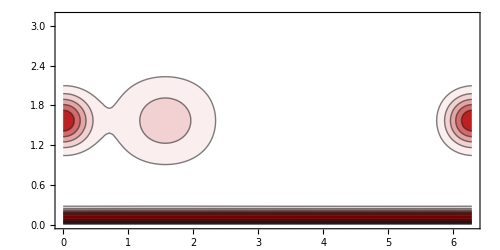

```mathematica
contourPlotOfDistributionOverSphericalShell[syntheticDataPDF["L"],1.0,PlotPoints->50]
```

#### plotCOMvectorTrio

```mathematica
plotCOMvectorTrio[ρSymbol_,h_,pIntervals_]:=Block[{COMs,s},
COMs=Table[
ρToCenterOfMass[
Table[Table[
ρSymbol[h,ℓ,m,pInt]
,{m,-ℓ,ℓ}],{ℓ,0,1}]
]
,{pInt,pIntervals}];
s=Mean[Norm/@COMs];

Show[{
Graphics3D[{
Darker[Red],
Table[{
Tube[{{0,0,0},0.9COM},0.02s],
Cone[{(1-0.15s)COM,COM},0.075s]
},{COM,COMs}],
Opacity[0.1],
Parallelepiped[{0,0,0},COMs]
}]
}
,SphericalRegion->True
,ImageSize->450
,PlotLabel->Det[COMs]
]
]
```

#### calculateρScaledMax

```mathematica
calculateρScaledMax[ρSymbol_,ℓmax_?IntegerQ]:=calculateρScaledMax[ρSymbol,{0,ℓmax}]

calculateρScaledMax[ρSymbol_,{ℓmin_,ℓmax_}]:=Max[Flatten[Table[Table[
(*{ℓ,m}->*)Abs[ρSymbol[ℓ,m]]^(1/Max[ℓ,1])
,{m,-ℓ,ℓ}],{ℓ,0,ℓmax}]]]
```

#### sphericalDecompositionPlot

```mathematica
Options[sphericalDecompositionPlot]={ColorFunction->ColorData["BlueGreenYellow"],Tolerance->10.^-5};
```

```mathematica
sphericalDecompositionPlot::usage="sphericalDecompositionPlot[ρSymbol,ℓmax] plots the spherical decomposition ρSymbol[ℓ,m].
sphericalDecompositionPlot[ρSymbol,ℓmax,{ℓ1,ℓ2,ℓ3}]";
```

```mathematica
sphericalDecompositionPlot[ρSymbol_,ℓmax_?IntegerQ,options:OptionsPattern[]]:=sphericalDecompositionPlot[ρSymbol,{0,ℓmax},options]
sphericalDecompositionPlot[ρSymbol_,{ℓmin_,ℓmax_},OptionsPattern[]]:=Block[{ρScaledMax},
ρScaledMax=calculateρScaledMax[ρSymbol,{ℓmin,ℓmax}];
Show[{
Table[
Table[
(*{ℓ,m}->*)Graphics[{
OptionValue[ColorFunction][Abs[ρSymbol[ℓ,m]]^(1/Max[ℓ,1])/ρScaledMax],
Tooltip[
Rectangle[{m-1/2,ℓ-1/2},{m+1/2,ℓ+1/2}]
,Row[{"ℓ=",ℓ,", m=",m,", |(ρ̃)_(ℓ, m)|^(1/ℓ)=",Abs[ρSymbol[ℓ,m]]^(1/Max[ℓ,1])/ρScaledMax}]]
}]
,{m,-ℓ,ℓ}]
,{ℓ,ℓmin,ℓmax}]
}
,Frame->True
,ImageSize->650
,PlotRangePadding->None
,AspectRatio->Automatic
,FrameLabel->{"m","ℓ"}
,PlotLabel->"|ρ_(ℓ, m)|^(1/max (ℓ, 1))"
]
]
```

```mathematica
sphericalDecompositionPlot[ρSymbol_,ℓmax_,{ℓ1_,ℓ2_,ℓ3_},options:OptionsPattern[]]:=sphericalDecompositionPlot[ρSymbol,{0,ℓmax},{ℓ1,ℓ2,ℓ3},options]

sphericalDecompositionPlot[ρSymbol_,{ℓmin_,ℓmax_},{ℓ1_,ℓ2_,ℓ3_},options:OptionsPattern[]]:=Block[{ρScaledMax,tolerance=OptionValue[Tolerance],CGρProduct,CGρProductMax},
ρScaledMax=calculateρScaledMax[ρSymbol,{ℓmin,ℓmax}];
CGρProductMax=Max[Flatten[Table[
CGρProduct[m1,m2]=Abs[Times[
Quiet[ClebschGordan[{ℓ1,m1},{ℓ2,m2},{ℓ3,m1+m2}],ClebschGordan::phy],
ρSymbol[ℓ1,m1],
ρSymbol[ℓ2,m2],
ρSymbol[ℓ3,m1+m2]//Conjugate
]]
,{m1,-ℓ1,ℓ1},{m2,-ℓ2,ℓ2}]]];

Show[{

sphericalDecompositionPlot[ρSymbol,{ℓmin,ℓmax},options],

Graphics[{
White,
PointSize[0.01],
Values@KeySortBy[Last]@Association@Table[
If[
CGρProduct[m1,m2]/CGρProductMax>=tolerance,
{m1,m2,CGρProduct[m1,m2]/CGρProductMax}->{
Tooltip[{
Blend[{{-ℓ2,Orange},{0,Blend[{{-ℓ1,Red},{ℓ1,Blue}},m1]},{ℓ2,Darker[Green]}},m2],
EdgeForm[{Opacity[CGρProduct[m1,m2]/CGρProductMax],Thickness[0.001]}],
FaceForm[Opacity[0.8CGρProduct[m1,m2]/CGρProductMax]],
Triangle[{{m1,ℓ1},{m2,ℓ2},{m1+m2,ℓ3}}],
Opacity[CGρProduct[m1,m2]/CGρProductMax],
Point[{{m1,ℓ1},{m2,ℓ2},{m1+m2,ℓ3}}],
}
,Row[{{m1,m2,m1+m2},"→",Round[CGρProduct[m1,m2]/CGρProductMax,0.01]}]]
}
,Nothing]
,{m1,-ℓ1,ℓ1},{m2,-ℓ2,ℓ2}]
}]
}]
]
```

#### RasterPlot3D

```mathematica
RasterPlot3D[data_,options___:OptionsPattern[]]:=Block[{reshapedData},
Show[{
Graphics3D[{
Raster3D[
Map[
#[[1,4]]&,
Map[
Values,
GroupBy[
data,
{#[[3]]&,#[[2]]&,#[[1]]&}
]
,{0,2}]
,{3}],
Transpose[Table[MinMax[data[[All,i]]],{i,1,3}]],
MinMax[data[[All,4]]]
,Evaluate[Sequence@@FilterRules[{options},Options[Raster3D]]]
,ColorFunction->Function[Directive[Opacity[0.15#,Black]]]
]
}]
}
,Evaluate[Sequence@@FilterRules[{options},Options[Show]]]
,Axes->True
,AxesLabel->{"p_x","p_y","p_z"}
,BoxRatios->Automatic
,SphericalRegion->True
,ImageSize->700
]
]
```

### Data exploration - raw from the previous work

```mathematica
ρ[h_,ℓ_,m_,{pmin_,pmax_}]:=ρ[h,ℓ,m,{pmin,pmax}]=Block[{data},
data=Select[firstFilterData[h],pmin<Norm[#[[1;;3]]]<pmax&];

1/nElec[h] Sum[
Block[{p,θ,ϕ,multiplicity},
{p,θ,ϕ}=ToSphericalCoordinates[record[[1;;3]]];
multiplicity=record[[4]];
multiplicity×p^ℓ SphericalHarmonicY[ℓ,m,θ,ϕ]
]
,{record,data}]

]
```

```mathematica
firstChiralityMeasure[h_,{pmin_,pmax_}]:=Sum[
If[Abs[m+n]<=4,
Times[
ClebschGordan[{2,m},{3,n},{4,m+n}],
ρ[h,2,m,{pmin,pmax}],
ρ[h,3,n,{pmin,pmax}],
ρ[h,4,m+n,{pmin,pmax}]*
],
0]
,{m,-2,2},{n,-3,3}]
```

```mathematica
firstChiralityMeasure["L",{0.5,0.6}]
```

0.-9.11319×10^-10 ⅈ

```mathematica
ListPlot[
Table[
{#1,Im[#2]}&@@@results1[[j]]
,{j,1,3}]
,PlotRange->All
,PlotStyle->{Darker[Blue,0.2],Darker[Red,0.2],Black}
,PlotLegends->LRA
,Frame->True
,ImageSize->500
,Joined->True
]
```

### SampleFunction

Write your package code here

```mathematica
SampleFunction::usage="This is a sample function for the Chimera template.";
Begin["`Private`"];
SampleFunction[x___]:="You have evaluated the Chimera sample function, SampleFunction, on the input "<>ToString[x]
End[];
```

## Package closure

### Package closure code

#### End of package

```mathematica
EndPackage[];
```

#### Add to distributed contexts.

```mathematica
DistributeDefinitions["Chimera`"];
```